## Determining Correction Vectors

```mathematica
DeviceResponse[x_]:=
(1/2)(0.5+ Tanh[(x-0.5)10]/2)+(1/2)x
```

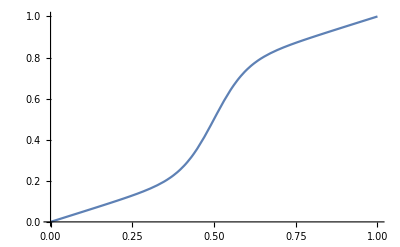

```mathematica
Plot[DeviceResponse[x],{x,0,1},PlotRange->{0,1}]
```

```mathematica
RealResponse[]:=
Module[
{a,b,c,d,xs,response,noise},
(xs=Range[0,1,0.001];
a=RandomVariate[NormalDistribution[]];
b=RandomVariate[NormalDistribution[]];
c=RandomVariate[NormalDistribution[]];
d=RandomVariate[NormalDistribution[]];
noise=RandomVariate[NormalDistribution[],Length@xs];
response=(1+0.1a)DeviceResponse[xs-0.02b]+(0.1)c xs^2+0.05d+0.01noise;
response
)]
```

```mathematica
dataSet=Table[RealResponse[],{25}];
```

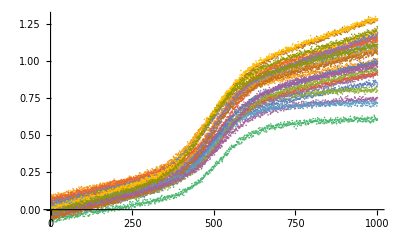

```mathematica
ListPlot[dataSet]
```

```mathematica
golden=GaussianFilter[#,20]&@Mean[dataSet];
```

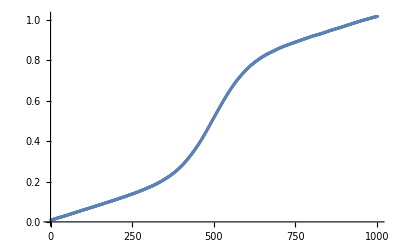

```mathematica
ListPlot[golden]
```

```mathematica
deviations=Map[(#-golden)&,#]&@dataSet;
```

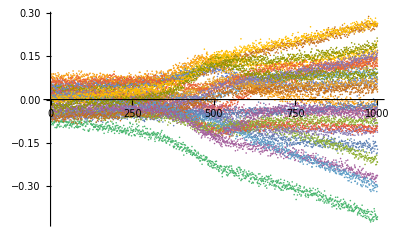

```mathematica
ListPlot[#,PlotRange->All]&@deviations
```

```mathematica
pcsRaw=Transpose@PrincipalComponents@Transpose@deviations;
```

```mathematica
pcsSmooth=Map[GaussianFilter[#,40]&,#]&@pcsRaw;
```

```mathematica
dcBasis=ConstantArray[1,Length@First@pcsSmooth];
```

```mathematica
allBasis=Prepend[#,dcBasis]&@pcsSmooth;
Dimensions@basis
```

{4,1001}

```mathematica
basisDepth=4;
```

```mathematica
basis=Part[#,1;;basisDepth]&@allBasis;
```

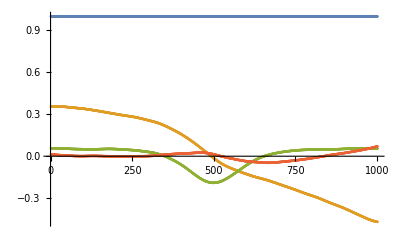

```mathematica
ListPlot[#,PlotRange->All]&@basis
```

## Device Fitting

```mathematica
device=RandomChoice@dataSet;
```

```mathematica
devVector=LeastSquares[Transpose@basis,device-golden]
```

{0.0553377,0.129069,-0.419134,0.160115}

```mathematica
deviceFit=golden+(Transpose@basis).devVector;
```

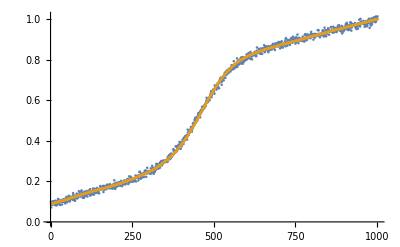

```mathematica
ListPlot[#]&@{device,deviceFit}
```